```mathematica
ClearAll["Global`*"]
```

```mathematica
elemlist=Table[i,{i,1,32}];
```

```mathematica
nx=Length[elemlist];
```

```mathematica
nu=0.001;
```

```mathematica
dx=(2*π)/Length[elemlist];
```

```mathematica
dt=0.01;
```

```mathematica
x[i_]:=-π+dx*i
```

```mathematica
ulist=Table[N[-Sin[x[i]]],{i,1,Length[elemlist]}];
```

```mathematica
ulistini=ulist;
```

```mathematica
ud[ulist_,i_]:=(ulist[[i+1]]-ulist[[i-1]])/(2.0*dx)
```

```mathematica
udd[ulist_,i_]:=(ulist[[i+1]]+ulist[[i-1]]-2.0*ulist[[i]])/dx^2
```

## Fixed Mesh

```mathematica
For[t=1,t≤8000,t++,rhslist1=Table[nu*udd[ulist,i]*dt-ulist[[i]]*ud[ulist,i]*dt,{i,2,nx-1}];rhslist1=Prepend[rhslist1,0.0];rhslist1=Append[rhslist1,0.0];u1list=ulist+dt*rhslist1;rhslist2=Table[nu*udd[u1list,i]*dt-u1list[[i]]*ud[u1list,i]*dt,{i,2,nx-1}];rhslist2=Prepend[rhslist2,0.0];rhslist2=Append[rhslist2,0.0];u2list=0.75*ulist+0.25*u1list+0.25*dt*rhslist2;rhslist3=Table[nu*udd[u2list,i]*dt-u2list[[i]]*ud[u2list,i]*dt,{i,2,nx-1}];rhslist3=Prepend[rhslist3,0.0];rhslist3=Append[rhslist3,0.0];ulist=1.0/3.0*ulist+2.0/3.0*u2list+2.0/3.0*dt*rhslist3;]
```

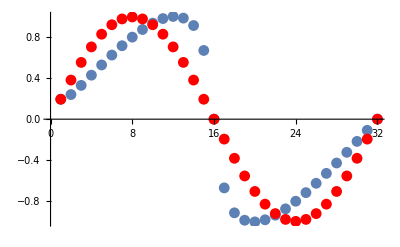

```mathematica
Show[ListPlot[ulist],ListPlot[ulistini,PlotStyle->Red]]
```

## Adding points

```mathematica
ClearAll["Global`*"]
```

```mathematica
nx=32;
```

```mathematica
elemlist=Table[i,{i,1,nx}];
```

```mathematica
xlist=Table[N[i/nx],{i,1,nx}];
```

```mathematica
nu=0.001;
```

```mathematica
dt=0.01;
```

```mathematica
ulist=Table[N[-Sin[x[i]]],{i,1,Length[elemlist]}];
```

```mathematica
ulistini=ulist;
```

```mathematica
dx[i_]:=x[i+1]-x[i];
```

```mathematica
ud[ulist_,i_]:=(ulist[[i+1]]-ulist[[i-1]])/(2.0*dx[i])
```

```mathematica
udd[ulist_,i_]:=(ulist[[i+1]]+ulist[[i-1]]-2.0*ulist[[i]])/dx[i]^2
```

```mathematica
For[t=1,t≤2,t++,rhslist1=Table[nu*udd[ulist,i]*dt-ulist[[i]]*ud[ulist,i]*dt,{i,2,nx-1}];rhslist1=Prepend[rhslist1,0.0];rhslist1=Append[rhslist1,0.0];u1list=ulist+dt*rhslist1;rhslist2=Table[nu*udd[u1list,i]*dt-u1list[[i]]*ud[u1list,i]*dt,{i,2,nx-1}];rhslist2=Prepend[rhslist2,0.0];rhslist2=Append[rhslist2,0.0];u2list=0.75*ulist+0.25*u1list+0.25*dt*rhslist2;rhslist3=Table[nu*udd[u2list,i]*dt-u2list[[i]]*ud[u2list,i]*dt,{i,2,nx-1}];rhslist3=Prepend[rhslist3,0.0];rhslist3=Append[rhslist3,0.0];ulist=1.0/3.0*ulist+2.0/3.0*u2list+2.0/3.0*dt*rhslist3;smoothlist=Table[Abs[ulist[[i+1]]-ulist[[i]]],{i,1,nx-1}];smoothlist=Append[smoothlist,0.0];nxnew=nx;unewlist=ulist;xnewlist=xlist;oldlength=Length[unewlist];
For[i=1,i≤nx,i++,If[smoothlist[[i]]>0.05,nxnew=nxnew+1;unewlist=Insert[unewlist,(ulist[[i]]+ulist[[i-1]])/2,i+Length[unewlist]-oldlength];xnewlist=Insert[xnewlist,(xlist[[i]]+xlist[[i-1]])/2,i+Length[unewlist]-oldlength]]];ulist=unewlist;
xlist=xnewlist;nx=nxnew;]
```